```mathematica
dir=NotebookDirectory[];
SetDirectory[dir];
file ="data06.csv";
data = Drop[Import[file,"Table","FieldSeparators"->";"],-13];
sdata = Drop[Take[data,{1,-1,20}],21];
timezero = sdata[[1,1]];
fdata=Table[{sdata[[i,1]]-timezero,sdata[[i,2]]}, {i, 1, Length[sdata]}];
time = Last[fdata] //First;
rb =Max[sdata];
amps = 0.6;
```

```mathematica
fdata;
sdata;
```

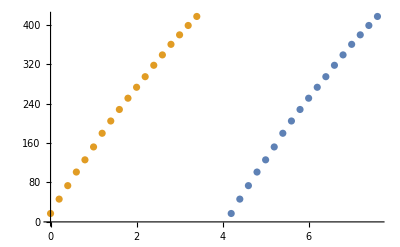

```mathematica
ListPlot[{sdata,fdata}]
```

Manual Approximation - Lower Boundary

```mathematica
mr = ρ t (r1^2-r2^2);
box = ρ t a b;
circle = ρ t r3^2;
motor = Quantity[100,"Grams" ("Centimeters")^2];
Θ =1/2 mr(r1^2+ r2^2)  + 3(1/12 box(a^2+ b^2) + box r^2)+ circle r3^2 +motor;
```

```mathematica
para = {r1 -> Quantity[98/2,"Millimeters"], r2 -> Quantity[92/2,"Millimeters"], t -> Quantity[5,"Millimeters"],ρ -> Quantity[7800,("Kilograms")/("Meters")^3],a -> Quantity[35,"Millimeters"],b -> Quantity[5,"Millimeters"], r -> Quantity[25,"Millimeters"],r3 -> Quantity[20/2,"Millimeters"]};
```

```mathematica
Θ /. para //N //UnitConvert
```

0.0000504229 kg m^2

Linear Approximation - Upper Boundary

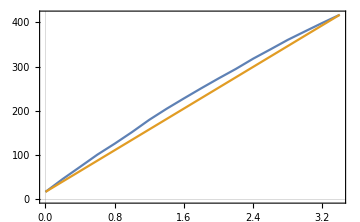

```mathematica
l[x_] := (sdata[[Length[fdata],2]]-sdata[[1,2]])/(sdata[[Length[fdata],1]] - sdata[[1,1]]) x
slopes =Table[ (sdata[[i,2]]-sdata[[1,2]])/(sdata[[i,1]]-sdata[[1,1]]) ,{i,2,Length[fdata]}];
line={fdata[[1]],fdata[[Length[sdata]]]};
ListLinePlot[{fdata,line},ImageSize->Medium,PlotRange->All,PlotTheme->"Scientific"]
```

| (τ a)/α, α → (ω2 -ω1)/(t2 -t1) |  Calculated and added through Inventor | Linear y == mx+b slope

```mathematica
interias =Quantity[Table[(0.0335 amps)/α /. α -> (sdata[[i,2]]-sdata[[1,2]])/(sdata[[i,1]]-sdata[[1,1]]) ,{i,5,Length[fdata]}]//Mean, "Kilograms" ("Meters")^2]
```

0.000157952 kg m^2

Manual NonLinear Fitting of ODE.

```mathematica
Manipulate[Plot[{ω+((a (1-ⅇ^(-(R t)/J)) τ)/R)/. {τ->0.0335, ω -> fdata[[1,2]]}}, {t,0,time},Epilog->{Red,Point[fdata]},ImageSize->Large],{J,1 10^-5,N@First[interias],Appearance -> {"Labeled"}},{{a,amps},0.1,amps+1,Appearance -> "Labeled"},{R,1 10^-5,1 10^-4,Appearance -> "Labeled"}]
```

Non-Linear Fitting of ODE.

```mathematica
model =FullSimplify[D[DSolve[{J ϕ''[t] == τ ai-R ϕ'[t] , ϕ[0] == 0,ϕ'[0] == fdata[[1,2]]},ϕ[t],t],t]]// First
fitting=NonlinearModelFit[fdata,ϕ'[t] /. model /. {τ->0.0335, ai -> amps},{{R, 1.6 10^-5},{J,1.4 10^-4}},t, Method->"Gradient"];
fitting["BestFitParameters"]
```

{ϕ'[t]→(1. ai τ+ⅇ^(-(R t)/J) (17.05 R-1. ai τ))/R}

{R→0.0000175204,J→0.000136125}

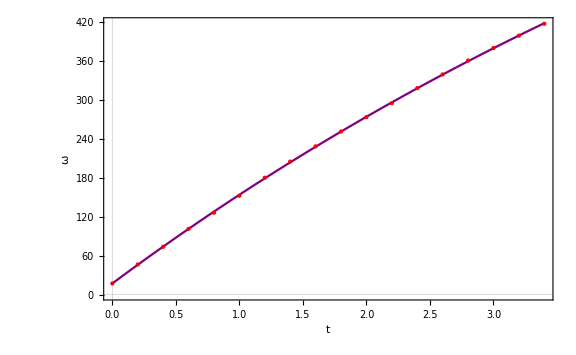

```mathematica
Plot[fitting[t], {t,0,time},Epilog->{PointSize[Medium],Red,Point[fdata]},Frame -> True,PlotTheme->"Scientific",FrameLabel->{"t","ω","Fitting"},RotateLabel->False,LabelStyle->FontSize->14,ImageSize->Large, PlotStyle->Purple]
```

```mathematica
mean =Mean[{{0.00016189710784190775},{0.00011856973682859183},{0.00012431225770767715}}]
```

{0.000134926}

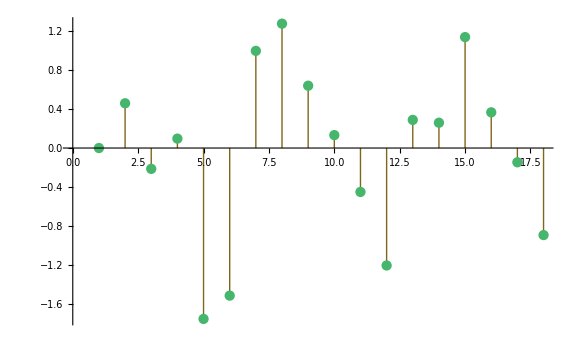

```mathematica
ListPlot[fitting["FitResiduals"],ImageSize->Large,Filling->Axis]
```

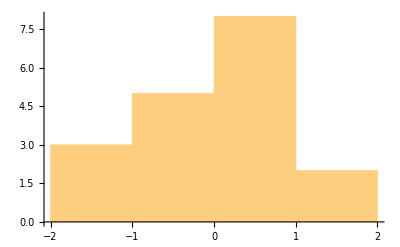

```mathematica
Histogram[fitting["FitResiduals"]]
```